note: difficult to do subsampling because signal is practically random.

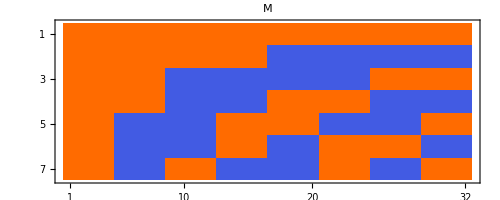

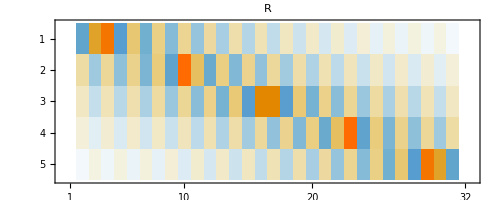

Rank S vs. nMeasurements vs. Full dim  {32,35,32}

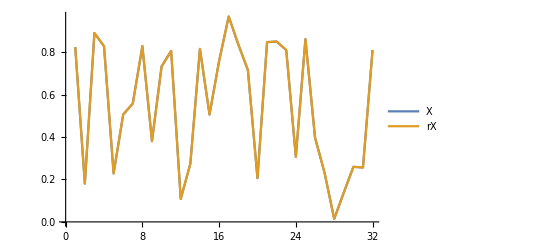

```mathematica
(* 1d singal *) 
dimSLM=32; dimCam=5; nMask=7;
(X = RandomReal[1,dimSLM])//MatrixForm//N;
(M = DiscreteHadamardTransform/@IdentityMatrix[dimSLM][[1;;nMask]])//MatrixPlot[#,PlotLabel->"M"]&
(R = ArrayResample[#,{dimCam},"Bin",Resampling->"Cubic"]&/@IdentityMatrix[dimSLM]//Transpose)//MatrixPlot[#, PlotLabel->"R"]&
(F=Fourier/@IdentityMatrix[dimSLM])//ComplexArrayPlot[#,PlotLabel->"F"]&;
(S=Outer[Times,M,R.F,1,1]//Flatten[#,1]&)//ComplexArrayPlot[#,PlotLabel->"S"]&;
Echo[{MatrixRank@S,nMask*Times@@dimCam,Times@@dimSLM},"Rank S vs. nMeasurements vs. Full dim"];
(Y=(S.X))//MatrixForm ;
(*(Y=Y+RandomReal[0.1,dimCam*nMask]);*)
(rX = PseudoInverse@S.Y)//MatrixForm//N;
ListLinePlot[{X,Abs@rX},PlotLegends->{"X", "rX"}]
```

{256,16,16}

ExampleData::obsolete: {TestImage,Lena} is being deprecated, and may not be available in future versions of the Wolfram Language.

Dim X  {256}

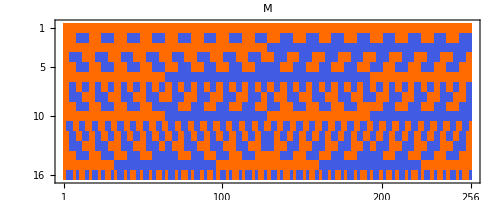

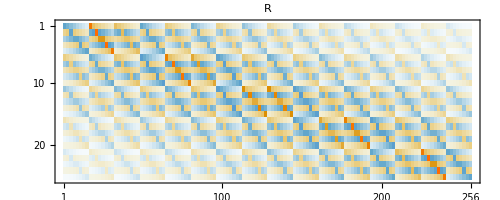

Rank S vs. nMeasurements vs. Full dim  {245,400,256}

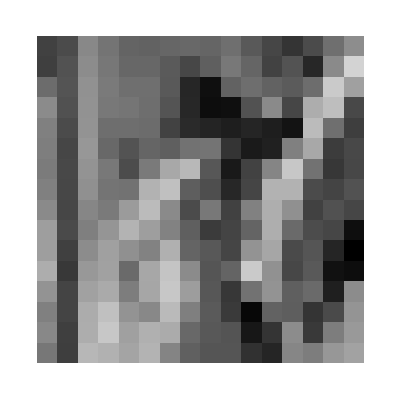
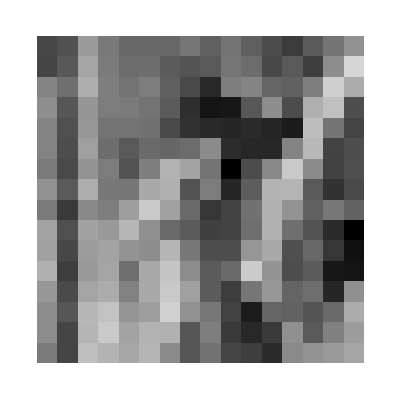

```mathematica
(* 2d singal *) 
dimSLM = {16,16}; dimCam = {5,5};nMask=16;
(basis = IdentityMatrix[Times@@dimSLM]//ArrayReshape[#, {Times@@dimSLM,dimSLM[[1]],dimSLM[[2]]} ]&)//Dimensions (* unsorted basis *)
(priority=Table[(i+j)^2+i,{i,0,dimSLM[[1]]-1},{j,0,dimSLM[[2]]-1}])//MatrixForm; (* triangle sorting *)
(sortedPriority=Sort[Flatten@priority]);
(priorityBasis=Outer[KroneckerDelta,sortedPriority,priority]//ArrayReshape[#,{Times@@dimSLM,dimSLM[[1]],dimSLM[[2]]}]&);
(wrap=Flatten[#,{{1},{2,3}}]&);
(X = ExampleData[{"TestImage", "Lena"}]//ImageResize[#,dimSLM]&//ColorConvert[#, "Grayscale"]&//ImageData//Flatten)//Echo[Dimensions@#, "Dim X"]&;
(M =((DiscreteHadamardTransform/@(priorityBasis[[1;;nMask]]))//wrap))//MatrixPlot[#,PlotLabel->"M"]&
(F =(Fourier/@basis)//Flatten[#,{2,3}]&)//ComplexArrayPlot[#, PlotLabel->"F"]&;
(R = (ArrayResample[#,dimCam,"Bin",Resampling->"Cubic"]&/@basis)//Flatten[#,{2,3}]&)//MatrixPlot[#, PlotLabel->"R"]&
(S=Outer[Times,M,R.F,1,1]//Flatten[#,1]&);
Echo[{MatrixRank@S,nMask*Times@@dimCam,Times@@dimSLM},"Rank S vs. nMeasurements vs. Full dim"];
(Y=(S.X));
(rX = PseudoInverse@S.Y)//MatrixForm//N;
{X,Abs@rX}//(ArrayPlot[ArrayReshape[#, dimSLM]]&)/@#&
```